```mathematica
sol = DSolve[{y'[x] + y[x] * Tan[x] == Sin[2 * x], y[0] == 2}, y[x], x]
```

{{y[x]→-2 (-2 Cos[x]+Cos[x]^2)}}

-Graphics-

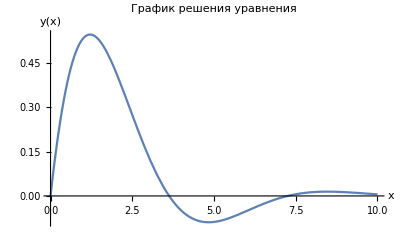

```mathematica
eqn=y''[x]+y[x]*Tan[x]==Sin[2*x];
sol=DSolve[{eqn,y[0]==2},y[x],x];
solfunc=y[x]/. sol[[1]];

check=Simplify[eqn/. y[x]->solfunc];
checkInitialCondition=Simplify[y[0]==2/. y[x]->solfunc];
Plot[solfunc,{x,0,2 Pi},PlotRange->All,AxesLabel->{"x","y(x)"},PlotLabel->"График решения уравнения"]

a=1;b=1;c=1; 
eqn=a*y''[x]+b*y'[x]+c*y[x]==0;
sol=DSolve[{eqn,y[0]==0,y'[0]==1},y[x],x];
solfunc=y[x]/. sol[[1]];

check=Simplify[eqn/. y[x]->solfunc];
checkInitialConditions=Simplify[{y[0]==0,y'[0]==1}/. y[x]->solfunc];

Plot[solfunc,{x,0,10},PlotRange->All,AxesLabel->{"x","y(x)"},PlotLabel->"График решения уравнения"]
```

```mathematica
m=1;b=0.5;c=1;A=1;ω=2; 
eqn=m*x''[t]+b*x'[t]+c*x[t]^2==A*Cos[ω*t];
sol=NDSolve[{eqn,x[0]==0,x'[0]==1},x,{t,0,10}];
solfunc=x[t]/. sol[[1]];

Plot[solfunc,{t,0,10},PlotRange->All,AxesLabel->{"t","x(t)"},PlotLabel->"График перемещения x(t)"]

(*График скорости x(t) груза*)
Plot[Evaluate[D[solfunc,t]],{t,0,10},PlotRange->All,AxesLabel->{"t","x'(t)"},PlotLabel->"График скорости x'(t)"]

ParametricPlot[Evaluate[{x[t],D[solfunc,t]}],{t,0,10},PlotRange->All,AxesLabel->{"x(t)","x'(t)"},PlotLabel->"Фазовый портрет"]

amplitude=Table[{ω,Max[Abs[x[t]/. NDSolve[{eqn,x[0]==0,x'[0]==1},x,{t,0,20}]]]},{ω,0.1,5,0.1}];
ListPlot[amplitude,Joined->True,AxesLabel->{"ω","Амплитуда"},PlotLabel->"Зависимость амплитуды от соотношения частот"]
```

NDSolve::ndsz: At t == 8.39257, step size is effectively zero; singularity or stiff system suspected.

-Graphics-

-Graphics-

InterpolatingFunction::dmval: Input value {8.57163} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {8.77571} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {8.9798} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

-Graphics-

NDSolve::ndsz: At t == 8.39257, step size is effectively zero; singularity or stiff system suspected.

General::stop: Further output of NDSolve::ndsz will be suppressed during this calculation.

-Graphics-

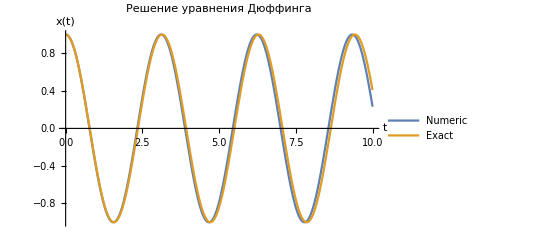

Solve::incnst: Inconsistent or redundant transcendental equation. After reduction, the bad equation is 1-Log[ⅇ^1] == 0.

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

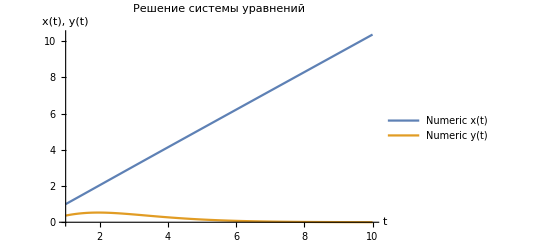

```mathematica
eps=0.1; 
eqn=x''[t]+4 x[t]+eps x[t]^3==0;
ic={x[0]==1,x'[0]==0};

solNumeric=NDSolve[{eqn,ic},x,{t,0,10}];

solExact=DSolve[{eqn/. eps->0,ic},x,{t,0,10}];

Plot[Evaluate[{x[t]/. solNumeric,x[t]/. solExact}],{t,0,10},PlotLegends->{"Numeric","Exact"},AxesLabel->{"t","x(t)"},PlotLabel->"Решение уравнения Дюффинга"]

eps=0.1; 
eqn={t*x'[t]==x[t]+eps*y[t],t*y'[t]==(2-x[t])*y[t]};
ic={x[1]==1,y[1]==1/E};

solNumeric=NDSolve[{eqn,ic},{x,y},{t,1,10}];

solExact=DSolve[{eqn/. eps->0,ic},{x,y},{t,1,10}];

Plot[Evaluate[{x[t],y[t]}/. solNumeric],{t,1,10},PlotLegends->{"Numeric x(t)","Numeric y(t)"},AxesLabel->{"t","x(t), y(t)"},PlotLabel->"Решение системы уравнений"]
```

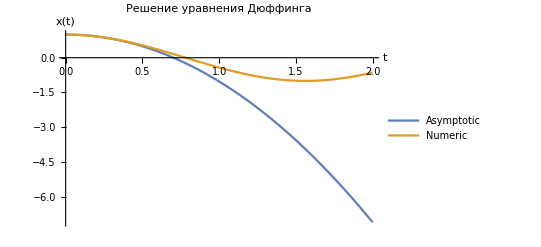

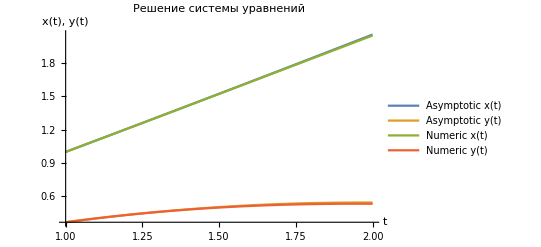

-Graphics-

```mathematica
eps=0.1; 
ω=2; 
b=0.5; 
a=1; 


solAsymptotic=AsymptoticDSolveValue[{x''[t]+ω^2*x[t]+eps*b*x[t]^3==0,x[0]==a,x'[0]==0},x[t],{t,0,2}];

solNumeric=NDSolve[{x''[t]+ω^2*x[t]+eps*b*x[t]^3==0,x[0]==a,x'[0]==0},x,{t,0,2}];

Plot[Evaluate[{solAsymptotic,x[t]/. solNumeric}],{t,0,2},PlotLegends->{"Asymptotic","Numeric"},AxesLabel->{"t","x(t)"},PlotLabel->"Решение уравнения Дюффинга"]

eps=0.1; 
ic={x[1]==1,y[1]==1/E};

solAsymptotic=AsymptoticDSolveValue[{t*x'[t]==x[t]+eps*y[t],t*y'[t]==(2-x[t])*y[t],ic},{x[t],y[t]},{t,1,2}];

solNumeric=NDSolve[{t*x'[t]==x[t]+eps*y[t],t*y'[t]==(2-x[t])*y[t],ic},{x,y},{t,1,2}];

Plot[Evaluate[{solAsymptotic,{x[t],y[t]}/. solNumeric}],{t,1,2},PlotLegends->{"Asymptotic x(t)","Asymptotic y(t)","Numeric x(t)","Numeric y(t)"},AxesLabel->{"t","x(t), y(t)"},PlotLabel->"Решение системы уравнений"]

eps=0.1; 
ic={x[1]==1,y[1]==1/E};

solAsymptotic=AsymptoticDSolveValue[{t*x'[t]==x[t]+eps*y[t],t*y'[t]==(2-x[t])*y[t],ic},{x[t],y[t]},{t,1,2}];

solNumeric=NDSolve[{t*x'[t]==x[t]+eps*y[t],t*y'[t]==(2-x[t])*y[t],ic},{x,y},{t,1,2}];

Plot[Evaluate[{solAsymptotic,{x[t],y[t]}/. solNumeric}],{t,1,2},PlotLegends->{"Asymptotic x(t)","Asymptotic y(t)","Numeric x(t)","Numeric y(t)"},AxesLabel->{"t","x(t), y(t)"},PlotLabel->"Решение системы уравнений"]
```